```mathematica
FvmBVP[n_,b_,δ_,f_,B_,uuu_]:=Module[{h,x,xd,xm,xm0,a,c0,dltt,u0,u00,u,var,varinit,eqn0,eqn1,eqn2,eqn,sol,A,T,i},
h=(b-δ)/n;xd=Table[δ+i h,{i,0,n-1}];
xm=Table[δ+(i+1/2) h,{i,0,n-1}];
xm0=δ-h/2;
u0=uexact[xd];u00=uexact[δ-h];
dltt=h;
u[n]=B;
var=Join[List[c0],Table[u[i],{i,1,n-1}]];
varinit=Transpose[{var,u0}];
u[-1]=uuu[δ-h,c0]//Simplify;
u[0]=uuu[xd[[1]],c0]//Simplify;
eqn0=(u[0]+u[-1])/2*(u[0]-u[-1])/h-(u[1]+u[0])/2*(u[1]-u[0])/h+1/(2*xm[[1]])*(u[0]^2+u[1]^2)/4-1/(2*xm0)*(u[0]^2+u[-1]^2)/4+h*u[0]^2/(4*xd[[1]]^2)-(f[xd[[1]],u[0]])*h;
eqn1=(u[i]+u[i-1])/2*(u[i]-u[i-1])/h-(u[i+1]+u[i])/2*(u[i+1]-u[i])/h+1/(2*xm[[i+1]])*(u[i]^2+u[i+1]^2)/4-1/(2*xm[[i]])*(u[i-1]^2+u[i]^2)/4+h*u[i]^2/(4*xd[[i+1]]^2)-(f[xd[[i+1]],u[i]])*h;
eqn=Join[List[eqn0==0],Table[eqn1==0,{i,1,n-1}]];
sol=FindRoot[eqn,varinit];
varinit=Transpose[{var,u0}];
u0=var/.sol;
a=u0[[1]];
u00=uuu[δ-h,a];
u0[[1]]=uuu[δ,a];
eqn2=Table[(u[i]+u[i-1])/2*(u[i]-u[i-1])/h-(u[i+1]+u[i])/2*(u[i+1]-u[i])/h+1/(2*xm[[i+1]])*(u[i]^2+u[i+1]^2)/4-1/(2*xm[[i]])*(u[i-1]^2+u[i]^2)/4+h*u[i]^2/(4*xd[[i+1]]^2)-(f[xd[[i+1]],u[i]])*h,{i,n-1}];
eqn=PrependTo[eqn2,eqn0];
A=D[eqn,{var}]/.sol;
T=Norm[A,2] Norm[Inverse[A],2];
{xd,u0,a,T}];
```

```mathematica
Clear["*"];
```

```mathematica
uexact[x_]:=(1-Cos[x])^(1/2);
```

```mathematica
δ=0.2;b=1;
udd[x_]=uexact[x];
B=udd[b]
```

√(1-Cos[1])

```mathematica
f[x_,u_]:=(u^2*(2 x )-2 x+Sin[x])/(4 x)
```

```mathematica
n=128
```

128

```mathematica
uuu[x_,c0_]:=(2*(c0 x^(3/2)+x^2/4-1/7 c0 x^(7/2)-x^4/48+1/154 c0 x^(11/2)+x^6/1440-(c0 x^(15/2))/6930-x^8/80640))^(1/2)
```

```mathematica
res=FvmBVP[n,b,δ,f,B,uuu]
```

Part::pkspec1: 表达式 1+i$3459 不能作为部分指定使用.

Part::pkspec1: 表达式 i$3459 不能作为部分指定使用.

Part::pkspec1: 表达式 1+i$3459 不能作为部分指定使用.

General::stop: 在本次计算中，Part::pkspec1 的进一步输出将被抑制.

{{0.2,0.20625,0.2125,0.21875,0.225,0.23125,0.2375,0.24375,0.25,0.25625,0.2625,0.26875,0.275,0.28125,0.2875,0.29375,0.3,0.30625,0.3125,0.31875,0.325,0.33125,0.3375,0.34375,0.35,0.35625,0.3625,0.36875,0.375,0.38125,0.3875,0.39375,0.4,0.40625,0.4125,0.41875,0.425,0.43125,0.4375,0.44375,0.45,0.45625,0.4625,0.46875,0.475,0.48125,0.4875,0.49375,0.5,0.50625,0.5125,0.51875,0.525,0.53125,0.5375,0.54375,0.55,0.55625,0.5625,0.56875,0.575,0.58125,0.5875,0.59375,0.6,0.60625,0.6125,0.61875,0.625,0.63125,0.6375,0.64375,0.65,0.65625,0.6625,0.66875,0.675,0.68125,0.6875,0.69375,0.7,0.70625,0.7125,0.71875,0.725,0.73125,0.7375,0.74375,0.75,0.75625,0.7625,0.76875,0.775,0.78125,0.7875,0.79375,0.8,0.80625,0.8125,0.81875,0.825,0.83125,0.8375,0.84375,0.85,0.85625,0.8625,0.86875,0.875,0.88125,0.8875,0.89375,0.9,0.90625,0.9125,0.91875,0.925,0.93125,0.9375,0.94375,0.95,0.95625,0.9625,0.96875,0.975,0.98125,0.9875,0.99375},{0.141188,0.145585,0.14998,0.154374,0.158766,0.163157,0.167546,0.171934,0.17632,0.180704,0.185086,0.189466,0.193845,0.198222,0.202597,0.206969,0.21134,0.215709,0.220075,0.22444,0.228802,0.233162,0.23752,0.241875,0.246229,0.250579,0.254927,0.259273,0.263616,0.267957,0.272295,0.27663,0.280963,0.285293,0.28962,0.293944,0.298266,0.302584,0.3069,0.311213,0.315522,0.319829,0.324132,0.328432,0.332729,0.337023,0.341313,0.3456,0.349884,0.354164,0.358441,0.362714,0.366984,0.37125,0.375513,0.379772,0.384027,0.388278,0.392526,0.39677,0.40101,0.405246,0.409478,0.413706,0.41793,0.42215,0.426366,0.430578,0.434785,0.438988,0.443187,0.447382,0.451572,0.455758,0.459939,0.464116,0.468288,0.472456,0.476619,0.480778,0.484932,0.489081,0.493225,0.497365,0.501499,0.505629,0.509754,0.513874,0.517988,0.522098,0.526203,0.530302,0.534397,0.538486,0.54257,0.546648,0.550721,0.554789,0.558852,0.562909,0.56696,0.571006,0.575046,0.579081,0.58311,0.587133,0.591151,0.595163,0.599169,0.603169,0.607164,0.611152,0.615134,0.619111,0.623081,0.627046,0.631004,0.634956,0.638902,0.642841,0.646774,0.650701,0.654622,0.658536,0.662444,0.666345,0.67024,0.674128},4.2952×10^-6,17853.4}

```mathematica
err=uexact[res[[1]]]-res[[2]]
```

{-2.70551×10^-6,-2.73874×10^-6,-2.76434×10^-6,-2.78327×10^-6,-2.79633×10^-6,-2.80423×10^-6,-2.80759×10^-6,-2.80694×10^-6,-2.80275×10^-6,-2.79543×10^-6,-2.78533×10^-6,-2.77279×10^-6,-2.75808×10^-6,-2.74145×10^-6,-2.72311×10^-6,-2.70327×10^-6,-2.6821×10^-6,-2.65975×10^-6,-2.63637×10^-6,-2.61207×10^-6,-2.58696×10^-6,-2.56116×10^-6,-2.53473×10^-6,-2.50778×10^-6,-2.48036×10^-6,-2.45253×10^-6,-2.42437×10^-6,-2.39592×10^-6,-2.36723×10^-6,-2.33834×10^-6,-2.30928×10^-6,-2.2801×10^-6,-2.25083×10^-6,-2.22148×10^-6,-2.1921×10^-6,-2.16269×10^-6,-2.13329×10^-6,-2.10391×10^-6,-2.07456×10^-6,-2.04527×10^-6,-2.01604×10^-6,-1.98689×10^-6,-1.95783×10^-6,-1.92887×10^-6,-1.90001×10^-6,-1.87127×10^-6,-1.84266×10^-6,-1.81417×10^-6,-1.78582×10^-6,-1.75761×10^-6,-1.72954×10^-6,-1.70162×10^-6,-1.67385×10^-6,-1.64624×10^-6,-1.61878×10^-6,-1.59148×10^-6,-1.56434×10^-6,-1.53737×10^-6,-1.51055×10^-6,-1.48391×10^-6,-1.45742×10^-6,-1.4311×10^-6,-1.40495×10^-6,-1.37897×10^-6,-1.35315×10^-6,-1.32749×10^-6,-1.302×10^-6,-1.27668×10^-6,-1.25152×10^-6,-1.22652×10^-6,-1.20169×10^-6,-1.17702×10^-6,-1.15251×10^-6,-1.12816×10^-6,-1.10397×10^-6,-1.07994×10^-6,-1.05607×10^-6,-1.03235×10^-6,-1.00879×10^-6,-9.85381×10^-7,-9.62125×10^-7,-9.39021×10^-7,-9.16068×10^-7,-8.93262×10^-7,-8.70605×10^-7,-8.48094×10^-7,-8.25727×10^-7,-8.03504×10^-7,-7.81423×10^-7,-7.59483×10^-7,-7.37683×10^-7,-7.1602×10^-7,-6.94495×10^-7,-6.73105×10^-7,-6.51849×10^-7,-6.30726×10^-7,-6.09734×10^-7,-5.88873×10^-7,-5.6814×10^-7,-5.47535×10^-7,-5.27056×10^-7,-5.06702×10^-7,-4.86472×10^-7,-4.66364×10^-7,-4.46377×10^-7,-4.2651×10^-7,-4.06762×10^-7,-3.87131×10^-7,-3.67617×10^-7,-3.48218×10^-7,-3.28932×10^-7,-3.09759×10^-7,-2.90698×10^-7,-2.71747×10^-7,-2.52906×10^-7,-2.34173×10^-7,-2.15546×10^-7,-1.97026×10^-7,-1.78611×10^-7,-1.60299×10^-7,-1.42091×10^-7,-1.23984×10^-7,-1.05977×10^-7,-8.80709×10^-8,-7.02632×10^-8,-5.25531×10^-8,-3.49399×10^-8,-1.74225×10^-8}

```mathematica
emax8=Max[Abs[err]]
```

0.00114269

```mathematica
emax16=Max[Abs[err]]
```

0.000217167

```mathematica
emax32=Max[Abs[err]]
```

0.0000485492

```mathematica
emax64=Max[Abs[err]]
```

0.0000115179

```mathematica
emax128=Max[Abs[err]]
```

2.80759×10^-6

```mathematica
Log2[{emax8/emax16,emax16/emax32,emax32/emax64,emax64/emax128}]
```

{2.39556,2.16128,2.07557,2.03647}

```mathematica
em8=Sqrt[Sum[(err[[i]])^2*(b-δ)/n,{i,1,n}]](*8*)
```

0.000591977

```mathematica
em16=Sqrt[Sum[(err[[i]])^2*(b-δ)/n,{i,1,n}]](*16*)
```

0.000115693

```mathematica
em32=Sqrt[Sum[(err[[i]])^2*(b-δ)/n,{i,1,n}]](*32*)
```

0.0000260077

```mathematica
em64=Sqrt[Sum[(err[[i]])^2*(b-δ)/n,{i,1,n}]](*64*)
```

6.18641×10^-6

```mathematica
em128=Sqrt[Sum[(err[[i]])^2*(b-δ)/n,{i,1,n}]](*128*)
```

1.50974×10^-6

```mathematica
Log2[{em8/em16,em16/em32,em32/em64,em64/em128}]
```

{2.35524,2.15329,2.07176,2.0348}

```mathematica
emh18=Sqrt[Sum[(err[[i]]-err[[i-1]])^2/((b-δ)/n),{i,2,n}]](*8*)
```

0.00128562

```mathematica
emh116=Sqrt[Sum[(err[[i]]-err[[i-1]])^2/((b-δ)/n),{i,2,n}]](*16*)
```

0.000247615

```mathematica
emh132=Sqrt[Sum[(err[[i]]-err[[i-1]])^2/((b-δ)/n),{i,2,n}]](*32*)
```

0.0000564639

```mathematica
emh164=Sqrt[Sum[(err[[i]]-err[[i-1]])^2/((b-δ)/n),{i,2,n}]](*64*)
```

0.0000136059

```mathematica
emh1128=Sqrt[Sum[(err[[i]]-err[[i-1]])^2/((b-δ)/n),{i,2,n}]](*128*)
```

3.34586×10^-6

```mathematica
Log2[{emh18/emh116,emh116/emh132,emh132/emh164,emh164/emh1128}]
```

{2.3763,2.1327,2.0531,2.02378}

```mathematica
emh8=0-res[[3]](*8*)
```

-0.00182144

```mathematica
emh16=0-res[[3]](*16*)
```

-0.00034503

```mathematica
emh32=0-res[[3]](*32*)
```

-0.0000756505

```mathematica
emh64=0-res[[3]](*64*)
```

-0.000017736

```mathematica
emh128=0-res[[3]](*128*)
```

-4.2952×10^-6

```mathematica
Log2[{emh8/emh16,emh16/emh32,emh32/emh64,emh64/emh128}]
```

{2.40028,2.1893,2.09267,2.04589}

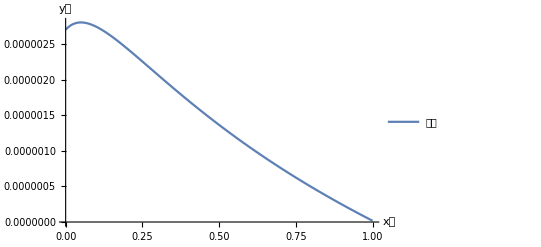

```mathematica
ListLinePlot[{Abs[err]},DataRange->{0,1},LabelStyle->{13,GrayLevel[0]},AxesLabel->{HoldForm[x轴],HoldForm[y轴]},PlotLegends->Placed[{"误差"},{Right,Top}]]
```

```mathematica
T8=64.58273206026462
```

64.5827

```mathematica
T16=263.06206807313794
```

263.062

```mathematica
T32=1076.9532132497834
```

1076.95

```mathematica
T64=4395.01038055551
```

4395.01

```mathematica
T128=17853.43942808611
```

17853.4